```mathematica
SetDirectory[NotebookDirectory[]];
```

#### To plot the stable and unstable regions

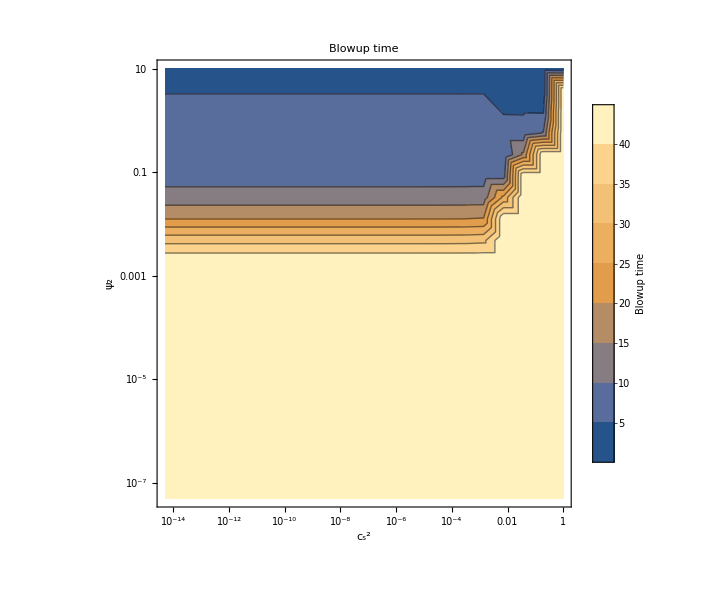

```mathematica
data=Import["./results.dat"];
ListContourPlot[data[[All,{1,2,3}]],TicksStyle->Directive[Orange,12],
ScalingFunctions->{"Log","Log"},PlotLabel->Style["Blowup time",FontSize->18],
FrameLabel->{Style["c_s^2",Black,22,Bold],Style["ψ_2",Black,22,Bold]},
FrameTicksStyle->Directive[FontSize->22,Black],
PlotLegends->{Placed[BarLegend[Automatic,LabelStyle->{FontSize->22,Black},LegendMarkerSize->500,LegendMargins->{{20,0},{40,0}},LegendLabel->Style["Blowup time",Black,22]],
Right]}, ImageSize->600]
```

```mathematica
data=Import["./Data/zfinal0Odarkenormalcs2near0.dat"];
ListContourPlot[data[[All,{1,2,3}]],TicksStyle->Directive[Orange,12],
ScalingFunctions->{"Log","Log"},PlotLabel->Style["Blowup time",FontSize->18],
FrameLabel->{Style["c_s^2",Black,22,Bold],Style["ψ_2",Black,22,Bold]},
FrameTicksStyle->Directive[FontSize->22,Black],
PlotLegends->{Placed[BarLegend[Automatic,LabelStyle->{FontSize->22,Black},LegendMarkerSize->500,LegendMargins->{{20,0},{40,0}},LegendLabel->Style["Blowup time",Black,22]],
Right]}, ImageSize->600]
```

-Graphics-

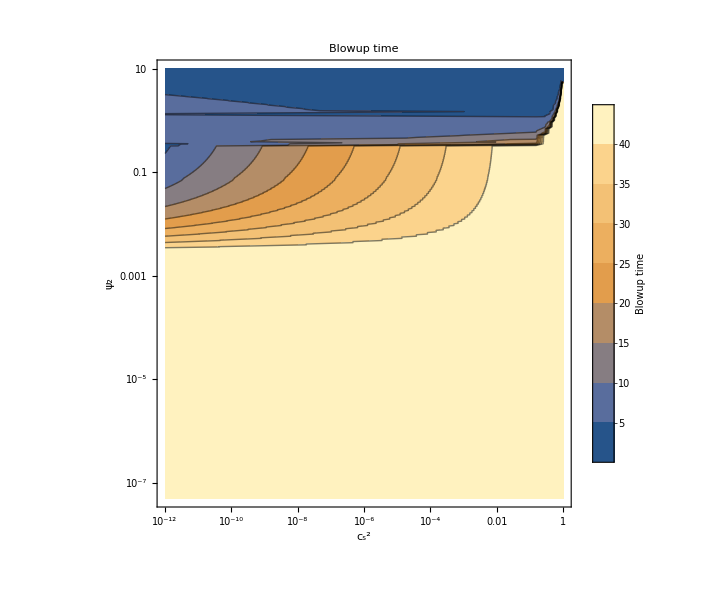

```mathematica
data=Import["./Data/zfinal0Odarkenormalcs2near1.dat"];
ListContourPlot[data[[All,{1,2,3}]],TicksStyle->Directive[Orange,12],
ScalingFunctions->{"Log","Log"},PlotLabel->Style["Blowup time",FontSize->18],
FrameLabel->{Style["c_s^2",Black,22,Bold],Style["ψ_2",Black,22,Bold]},
FrameTicksStyle->Directive[FontSize->22,Black],
PlotLegends->{Placed[BarLegend[Automatic,LabelStyle->{FontSize->22,Black},LegendMarkerSize->500,LegendMargins->{{20,0},{40,0}},LegendLabel->Style["Blowup time",Black,22]],
Right]}, ImageSize->600]
```

```mathematica
data=Import["./Data/zfinal0Odarkenormalcs2uniform.dat"];
ListContourPlot[data[[All,{1,2,3}]],TicksStyle->Directive[Orange,12],
ScalingFunctions->{"Log","Log"},PlotLabel->Style["Blowup time",FontSize->18],
FrameLabel->{Style["c_s^2",Black,22,Bold],Style["ψ_2",Black,22,Bold]},
FrameTicksStyle->Directive[FontSize->22,Black],
PlotLegends->{Placed[BarLegend[Automatic,LabelStyle->{FontSize->22,Black},LegendMarkerSize->500,LegendMargins->{{20,0},{40,0}},LegendLabel->Style["Blowup time",Black,22]],
Right]}, ImageSize->600]
```

-Graphics-